```mathematica
(*Equations A.6 and A.7  n=1*)
Clear[mh,dmh,mw,rhoInit,FInit,GInit,dFdrhoInit,dGdrhoInit,rhoTarg,FTarg,GTarg]
mh:=√2
dmh:=0
mw:=mh/2
eqF:=F''[r]-2*mh*F'[r]+mh/(4*r)*(G[r])^2
eqG:=G''[r]-mh*G'[r]-2/r^2*G[r]+mh/(4*r)*ⅇ^(-mh*r)*F[r]*G[r]
rhoInit:=10(*9.998*)
FInit:=983.680305(*1011.5015*)
GInit:=95.343486(*93.1839*)
dFdrhoInit:=1108.284
dGdrhoInit:=23.292
rhoTarg[1]:=6.9980
FTarg[1]:=737.149191
GTarg[1]:=98.180481
rhoTarg[2]:=4.017
FTarg[2]:=309.400021
GTarg[2]:=85.650071
rhoTarg[3]:=0.997
FTarg[3]:=8.175800
GTarg[3]:=5.542144
rhoTarg[4]:=1.4030
FTarg[4]:=18.3540
GTarg[4]:=12.3593
```

```mathematica
i:=4
sol = NDSolve[{eqF==0,eqG==0,F[rhoInit]==FInit,G[rhoInit]==GInit,F[rhoTarg[i]]==FTarg[i],G[rhoTarg[i]]==GTarg[i]},{F,G},r, Method->{"Shooting","StartingInitialConditions"->{F[rhoInit]==FInit,G[rhoInit]==GInit,F'[rhoInit]==dFdrhoInit,G'[rhoInit]==dGdrhoInit}}];
```

NDSolve::ndsz: At r == 5.50548, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 3.28363, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.57341, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: "ndsz" will be suppressed during this calculation.

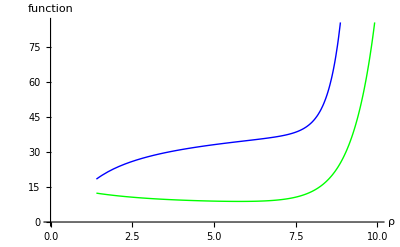

```mathematica
Plot[{Evaluate[F[r] /. sol],Evaluate[G[r] /. sol]}, {r,rhoTarg[i],rhoInit},PlotStyle->{Blue,Green},AxesLabel->{ρ,function},AxesOrigin->{0,0}]
(*F[rho] is blue  G[rho] is green*)
```

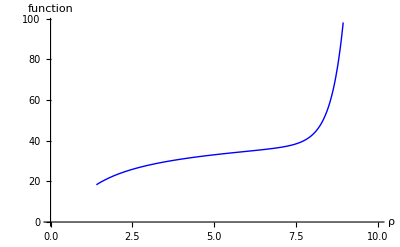

```mathematica
Plot[{Evaluate[F[r] /. sol]}, {r,rhoTarg[i],rhoInit},PlotStyle->{Blue},AxesLabel->{ρ,function},AxesOrigin->{0,0}]
```

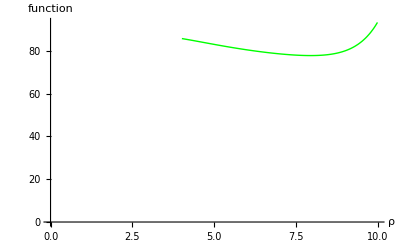

```mathematica
Plot[{Evaluate[G[r] /. sol]}, {r,rhoTarg[i],rhoInit},PlotStyle->{Green},AxesLabel->{ρ,function},AxesOrigin->{0,0}]
```